```mathematica
<< Rlink`
```

```mathematica
InstallR[]
```

```mathematica
REvaluate["load(paste(\"~/Rtmp\",\"diamonds.rdata\",sep=\"/\"))"]
```

diamonds

```mathematica
carat =REvaluate["diamonds$carat"];
price = REvaluate["diamonds$price"];
```

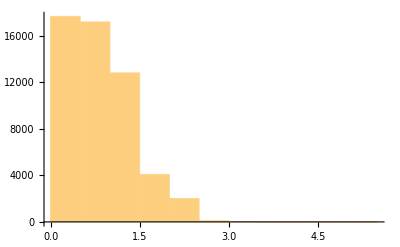

```mathematica
Histogram[carat,{.5}]
```

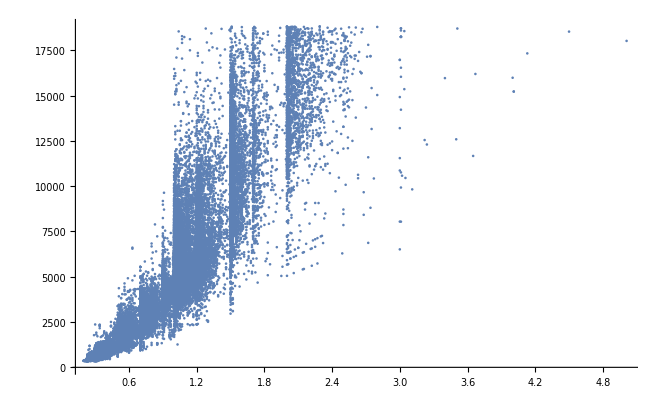

```mathematica
ListPlot[Thread[{carat,price}],PlotRange->Full]
```

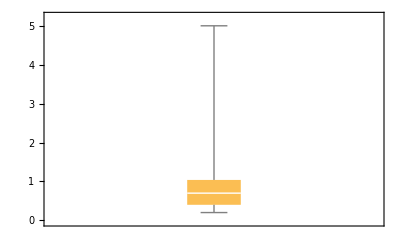

```mathematica
BoxWhiskerChart[carat]
```

```mathematica
ListDensityPlot[carat]
```

ListDensityPlot::arrayerr: {0.23, 0.21, 0.23, 0.29, 0.31, 0.24, 0.24, 0.26, 0.22, 0.23, 0.3, 0.23, 0.22, 0.31, 0.2, 0.32, 0.3, 0.3, 0.3, 0.3, 0.3, 0.23, 0.23, 0.31, 0.31, 0.23, 0.24, 0.3, 0.23, 0.23, 0.23, 0.23, 0.23, 0.23, 0.23, 0.23, 0.23, 0.31, 0.26, 0.33, 0.33, 0.33, 0.26, 0.26, 0.32, 0.29, 0.32, 0.32, 0.25, 0.29, « 53890 »} must be a valid array.

ListDensityPlot[{0.23,0.21,0.23,0.29,0.31,0.24,0.24,0.26,0.22,0.23,0.3,0.23,0.22,0.31,0.2,0.32,0.3,0.3,0.3,0.3,0.3,0.23,0.23,0.31,0.31,0.23,53888,0.84,0.77,0.74,0.9,0.76,0.76,0.7,0.7,0.7,0.73,0.73,0.79,0.71,0.79,0.79,0.71,0.71,0.71,0.7,0.7,0.72,0.72,0.72,0.7,0.86,0.75}]
 |  |  |  |

```mathematica
Length@Range[0,4.9,.1]
```

50

```mathematica
Length@N@Rescale@BinCounts[carat,.1]
```

50

```mathematica
caratDensity=Interpolation[Thread[{Range[0,4.9,.1],N@Rescale@BinCounts[carat,.1]}]]
```

InterpolatingFunction[{{0., 4.9}}, <>]

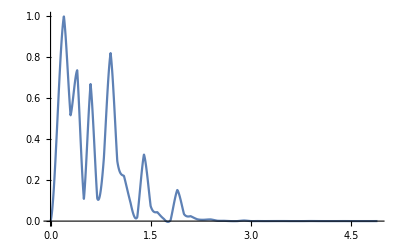

```mathematica
Plot[caratDensity[x],{x,0,4.9},PlotRange->Full]
```